```mathematica
(*Initialisation - Run first*)
SetEnvironment["OMP_NUM_THREADS"->"8"]
(*Replace the following with the appropriate pathways for your device*)
Import["/Users/questuser/Documents/QuESTlink/Link/QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["/Users/questuser/Documents/Kathryn/quest_link"]; (*Creating QuEST environment*)
Import["/Users/questuser/Documents/Kathryn/RydbergGerardCZDCSWAP.wl"]; (*Configuration File*)
data=Import["/Users/questuser/Documents/Kathryn/BV12Q.csv"]; 
userconfig=<|
NQubits-> 13,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,12],{{1,1,0},{3,2,0},{3,0,0},{4,2,0},{4,0,0},{5,2,0},{5,0,0},{0,2,0},{0,0,0},{1,2,0},{1,0,0},{2,2,0},{2,0,0}}}](*,{1,2,0}}}]*),
(* blockade radius in μm*)
BlockadeRadius->Sqrt[2],
(*BlockadeRadius->3,*)
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 98,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];
RydDev[Gates][[All,1]]
RydDev[InitLocations]

data[[5]];
d=data[[5]][[3;;data[[2,1]]+2]];
Length[data]
Fraction[a_,b_]:=a/b
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations]
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
```

{Init_q$_Integer,Wait_qubits$__[dur$_]/;Complement[Flatten[{qubits$}],Range[0,userconfig[NQubits]-1]]==={},M_q$_Integer,SRot_q$_Integer[ϕ$_,Δ$_,tg$_],H_q$_Integer,Rx_q$_Integer[θ$_],Ry_q$_Integer[θ$_],Rz_q$_Integer[θ$_],SWAP_(q1$_Integer,q2$_Integer),SWAPLoc_(q1$_Integer,q2$_Integer),ShiftLoc_q$__[v$_]/;LegitShift[Flatten[{q$}],qubitLocs$207174,v$],CZ_(p$_Integer,q$_Integer)[ϕ$_]/;blockadeCheck$207174[{p$,q$}],C_c$_[Z_t$__]/;blockadeCheck$207174[{c$,t$}],C_c$_[Z_t$__[θ$_]]/;blockadeCheck$207174[{c$,t$}],C_c$__[Z_t$_]/;blockadeCheck$207174[{c$,t$}],C_c$__[Z_t$_[θ$_]]}

-Graphics3D-

8188

<|0→{1,1,0},1→{3,2,0},2→{3,0,0},3→{4,2,0},4→{4,0,0},5→{5,2,0},6→{5,0,0},7→{0,2,0},8→{0,0,0},9→{1,2,0},10→{1,0,0},11→{2,2,0},12→{2,0,0}|>

```mathematica
InsertCircuitNoise[{Subscript[ShiftLoc, 0][{3,0,0}]},RydDev];
RydDev[QubitLocations]
RydDev[PlotAvailQubits][]
Reg=CreateDensityQureg[2];
InitClassicalState[Reg,3];
ApplyCircuit[Reg,ExtractCircuit[GetCircuitSchedule[{Subscript[CZ, 1,0][Pi]},RydDev,ReplaceAliases->True]]]
CalcProbOfAllOutcomes[Reg,{0,1}]
?ShiftLoc
```

<|0→{1,1,0},1→{3,2,0},2→{3,0,0},3→{4,2,0},4→{4,0,0},5→{5,2,0},6→{5,0,0},7→{0,2,0},8→{0,0,0},9→{1,2,0},10→{1,0,0},11→{2,2,0},12→{2,0,0}|>

-Graphics3D-

{}

{0.,0.,0.,1.}

16

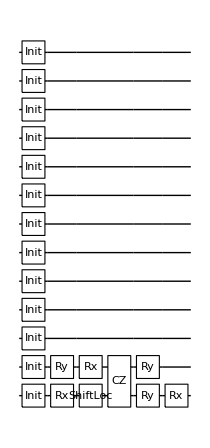
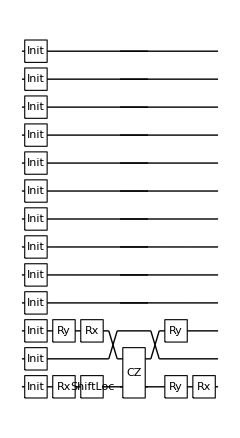
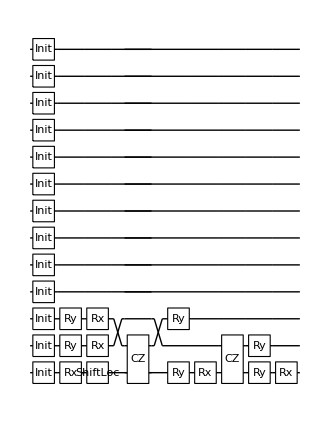
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
CircuitTranslator[DataSet_]:=Table[CircSplit=DataSet[[i,3;;DataSet[[i,1]]+2]];
(*Print[CircSplit];*)ZonesMoved=0;
Join[Table[Subscript[Init, j],{j,0,userconfig[NQubits]-1}],Flatten[Table[GateSplit=StringSplit[CircSplit[[j]],", ["];
GateName=StringTrim[StringTrim[GateSplit[[1]],"["],"'"];
GateQubits=IntegerPart[ToExpression[StringSplit[StringTrim[GateSplit[[2]],"]"],","]]];
GateParameters=If[StringContainsQ[GateName,"C"],Pi,Pi*ToExpression[StringReplace[StringTrim[GateSplit[[3]],"]]"],{"("->"[",")"->"]"}]]];
If[Length[GateQubits]==2,If[GateQubits[[1]]<=(userconfig[NQubits]-1)-6*(ZonesMoved+1),MoveSize=((userconfig[NQubits]-1)-Ceiling[GateQubits[[1]],6])/2;ZonesMoved+=MoveSize/3;{Subscript[ShiftLoc, 0][{MoveSize,0,0}],Subscript[ToExpression[GateName],GateQubits[[1]],GateQubits[[2]]][GateParameters]},Subscript[ToExpression[GateName],GateQubits[[1]],GateQubits[[2]]][GateParameters]],Subscript[ToExpression[GateName], GateQubits[[1]]][GateParameters]],{j,1,DataSet[[i,1]]}]]]
,{i,1,Length[DataSet]}]
(*a=data[[2;;Length[data]]][[1]][[3;;9]]*)
Circs=CircuitTranslator[data];
Table[(*ExtractCircuit[InsertCircuitNoise[*)DrawCircuit[Circs[[i]]](*,RydDev,ReplaceAliases->True]]*),{i,1,4}]
```

```mathematica
{Subscript[Init, q$_Integer],Subscript[Wait, qubits$__][dur$_]/;Complement[Flatten[{qubits$}],Range[0,userconfig[NQubits]-1]]==={},Subscript[M, q$_Integer],Subscript[SRot, q$_Integer][ϕ$_,Δ$_,tg$_],Subscript[H, q$_Integer],Subscript[Rx, q$_Integer][θ$_],Subscript[Ry, q$_Integer][θ$_],Subscript[Rz, q$_Integer][θ$_],Subscript[SWAP, q1$_Integer,q2$_Integer],Subscript[SWAPLoc, q1$_Integer,q2$_Integer],Subscript[ShiftLoc, q$__][v$_]/;LegitShift[Flatten[{q$}],qubitLocs$1852814,v$],Subscript[CZ, p$_Integer,q$_Integer][ϕ$_]/;blockadeCheck$1852814[{p$,q$}],Subscript[C, c$_][Subscript[Z, t$__]]/;blockadeCheck$1852814[{c$,t$}],Subscript[C, c$_][Subscript[Z, t$__][θ$_]]/;blockadeCheck$1852814[{c$,t$}],Subscript[C, c$__][Subscript[Z, t$_]]/;blockadeCheck$1852814[{c$,t$}],Subscript[C, c$__][Subscript[Z, t$_][θ$_]]}
```

```mathematica
KetList[NQ_]:=Table[ToExpression@StringSplit[IntegerString[i,2,NQ],""],{i,0,2^NQ-1,1}]
KetList[2]
Length[%]
RydDev[PlotAvailQubits][]
```

{{0,0},{0,1},{1,0},{1,1}}

4

-Graphics3D-

```mathematica
{"0000","0001","0010","0011","0100","0101","0110","0111","1000","1001","1010","1011","1100","1101","1110","1111"}
```

16

```mathematica
percent2infidel[num_]:=Module[{},Assert[0<=num<=100,"number is in percent"];1-0.01 num];
Circs=CircuitTranslator[data];
```

```mathematica
MeasErrors[QubitList_]:=Table[Subscript[Depol, QubitList[[i]]][percent2infidel[userconfig[FidMeas]]],{i,1,Length[QubitList]}]
MeasBuilder[QuReg_,QubitList_]:=Table[CalcProbOfOutcome[QuReg,QubitList[[i]],0],{i,1,Length[QubitList]}]
(*BVCircuitApplier[Circs_,ρ_,Nq_]:= Table[InitZeroState[ρ];ApplyCircuit[ρ,Join[ExtractCircuit[InsertCircuitNoise[Join[Table[Subscript[Init, j],{j,0,Nq-1}],Circs[[i]]],RydDev,ReplaceAliases->True]],Flatten[Table[{Subscript[Depol, q][1-0.01*99.7] ,ExtractCircuit[InsertCircuitNoise[{Subscript[Wait, q][2*10^4]},RydDev,ReplaceAliases->True]]},{q,1,Nq-1}]]]];Res=CalcProbOfAllOutcomes[ρ,Range[1,Nq-1]]
,{i,1,Length[Circs]}]*)
BVCircuitApplier[Circs_,ρ_,Nq_]:= Table[If[ContainsAny[Circs[[i]],{Subscript[ShiftLoc, 0][{3,0,0}],Subscript[ShiftLoc, 0][{6,0,0}]}],SplitCirc=SequenceSplit[Circs[[i]],{Subscript[ShiftLoc, 0][{3,0,0}]}];Print[SplitCirc];ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[SplitCirc[[1]],RydDev,ReplaceAliases->True]]];InsertCircuitNoise[{Subscript[ShiftLoc, 0][{3,0,0}]},RydDev];
Print[RydDev[PlotAvailQubits][]];ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[SplitCirc[[1]],RydDev,ReplaceAliases->True]]];InsertCircuitNoise[{Subscript[ShiftLoc, 0][{-3,0,0}]},RydDev];,ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Circs[[i]],RydDev,ReplaceAliases->True]]]];
ApplyCircuit[ρ,MeasErrors[Reverse[Range[1,Nq-1]]]];
P0s=MeasBuilder[ρ,Reverse[Range[1,Nq-1]]]; P1s=ConstantArray[1,Length[P0s]]-P0s;Pops=Table[PSeed=KetList[Nq-1][[j]];ProbSeed=P1s*PSeed +P0s*(PSeed/.{0->1,1->0});
Times@@ProbSeed,{j,1,2^(Nq-1)}];

{Pops,Max[Flatten[Position[Pops,RankedMax[Pops,2]]]]},
{i,1,Length[Circs]}]
ρ=CreateDensityQureg[13];
InitClassicalState[ρ,8190]
i=1
RydDev[PlotAvailQubits][]
Table[Print[Nq];Probs=BVCircuitApplier[Circs[[i;;i+2^(Nq-1)-1]],ρ,Nq];i=i+2^(Nq-1);Probs,{Nq,3,3}]
```

1

1

-Graphics3D-

3

{{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Init_6,Init_7,Init_8,Init_9,Init_10,Init_11,Init_12,Rx_0[-π],Ry_1[π/2],Rx_1[π]},{CZ_(1,0)[π],Ry_0[-π],Rx_0[-π],Ry_1[π/2]}}

-Graphics3D-

{{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Init_6,Init_7,Init_8,Init_9,Init_10,Init_11,Init_12,Rx_0[-π],Ry_2[π/2],Rx_2[π]},{CZ_(2,0)[π],Ry_0[-π],Rx_0[-π],Ry_2[π/2]}}

-Graphics3D-

{{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Init_6,Init_7,Init_8,Init_9,Init_10,Init_11,Init_12,Rx_0[-π],Ry_1[π/2],Rx_1[π],Ry_2[π/2],Rx_2[π]},{CZ_(2,0)[π],Ry_0[-π],Rx_0[-π],CZ_(1,0)[π],Ry_0[-π],Rx_0[-π],Ry_1[π/2],Ry_2[π/2]}}

-Graphics3D-

{{{{0.811001,0.089555,0.089555,0.00988912},3},{{0.285221,0.465003,0.09496,0.154816},1},{{0.197944,0.118773,0.427044,0.256239},4},{{0.0696151,0.194232,0.194232,0.541922},3}}}